```mathematica
A=440;
```

```mathematica
Py={1,256/243,9/8, 32/27,81/64, 4/3, 729/512,3/2, 128/81,27/16,16/9, 243/128}
```

{1,256/243,9/8,32/27,81/64,4/3,729/512,3/2,128/81,27/16,16/9,243/128}

```mathematica
f[a_]:=Piecewise[{{a,a<2},{a/2,a≥2},{a/4, a≥4}}]
```

```mathematica
Py8=Table[1.0*Py[[i]]*Py[[8]], {i, 1,12}];
Py8=Map[f , Py8];
Py8=Sort[Py8]

F[a_]:=Sort[Map[f, Table[Py[[i]]*Py[[a]],{i,1,12}]]];
```

{1.,1.06787,1.125,1.18519,1.26563,1.33333,1.42383,1.5,1.58025,1.6875,1.77778,1.89844}

```mathematica
1.0*F[7]
```

{1.01364,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
M=Table[1.0*F[i]/F[i][[1]], {i,1,12}];
MatrixForm[%]
```

(1. | 1.0535 | 1.125 | 1.18519 | 1.26563 | 1.33333 | 1.42383 | 1.5 | 1.58025 | 1.6875 | 1.77778 | 1.89844
1. | 1.0535 | 1.10986 | 1.18519 | 1.24859 | 1.33333 | 1.40466 | 1.5 | 1.58025 | 1.66479 | 1.77778 | 1.87289
1. | 1.06787 | 1.125 | 1.18519 | 1.26563 | 1.33333 | 1.42383 | 1.5 | 1.60181 | 1.6875 | 1.77778 | 1.89844
1. | 1.0535 | 1.125 | 1.18519 | 1.24859 | 1.33333 | 1.40466 | 1.5 | 1.58025 | 1.6875 | 1.77778 | 1.87289
1. | 1.06787 | 1.125 | 1.20135 | 1.26563 | 1.33333 | 1.42383 | 1.5 | 1.60181 | 1.6875 | 1.80203 | 1.89844
1. | 1.0535 | 1.125 | 1.18519 | 1.26563 | 1.33333 | 1.40466 | 1.5 | 1.58025 | 1.6875 | 1.77778 | 1.89844
1. | 1.0535 | 1.10986 | 1.18519 | 1.24859 | 1.33333 | 1.40466 | 1.47981 | 1.58025 | 1.66479 | 1.77778 | 1.87289
1. | 1.06787 | 1.125 | 1.18519 | 1.26563 | 1.33333 | 1.42383 | 1.5 | 1.58025 | 1.6875 | 1.77778 | 1.89844
1. | 1.0535 | 1.125 | 1.18519 | 1.24859 | 1.33333 | 1.40466 | 1.5 | 1.58025 | 1.66479 | 1.77778 | 1.87289
1. | 1.06787 | 1.125 | 1.20135 | 1.26563 | 1.33333 | 1.42383 | 1.5 | 1.60181 | 1.6875 | 1.77778 | 1.89844
1. | 1.0535 | 1.125 | 1.18519 | 1.26563 | 1.33333 | 1.40466 | 1.5 | 1.58025 | 1.6875 | 1.77778 | 1.87289
1. | 1.06787 | 1.125 | 1.20135 | 1.26563 | 1.35152 | 1.42383 | 1.5 | 1.60181 | 1.6875 | 1.80203 | 1.89844)

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0151421 | 0. | -0.0170348 | 0. | -0.0191642 | 0. | 0. | -0.0227131 | 0. | -0.0255523
0. | 0.0143732 | 0. | 0. | 0. | 0. | 0. | 0. | 0.0215597 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0170348 | 0. | -0.0191642 | 0. | 0. | 0. | 0. | -0.0255523
0. | 0.0143732 | 0. | 0.0161698 | 0. | 0. | 0. | 0. | 0.0215597 | 0. | 0.0242547 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0191642 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0151421 | 0. | -0.0170348 | 0. | -0.0191642 | -0.0201894 | 0. | -0.0227131 | 0. | -0.0255523
0. | 0.0143732 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0170348 | 0. | -0.0191642 | 0. | 0. | -0.0227131 | 0. | -0.0255523
0. | 0.0143732 | 0. | 0.0161698 | 0. | 0. | 0. | 0. | 0.0215597 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0191642 | 0. | 0. | 0. | 0. | -0.0255523
0. | 0.0143732 | 0. | 0.0161698 | 0. | 0.018191 | 0. | 0. | 0.0215597 | 0. | 0.0242547 | 0.)

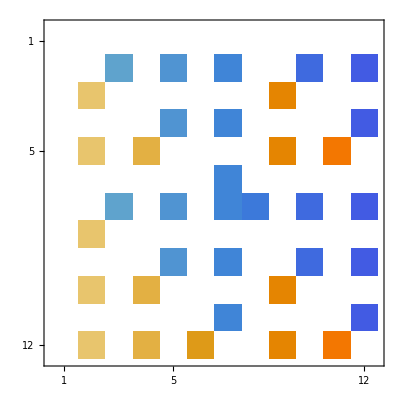

```mathematica
DiffM=Table[1.0*(F[i]/F[i][[1]]-F[1]), {i,1,12}];
MatrixForm[%]
MatrixPlot[%]
```